14/02/2015
Find vector plot of points in x-η plane

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
fL[x_]:=(1-HeavisideTheta[x+X]-HeavisideTheta[x-X]);
ηproc=OrnsteinUhlenbeckProcess[0,θ,σ,0];
xQproc=StratonovichProcess[ⅆx[t]==-1*b x ⅆt+ⅆη[t],
x[t],{x,0},t,η\[Distributed]ηproc];
xLproc=StratonovichProcess[ⅆx[t]==b X fL[x]ⅆt+ⅆη[t],
x[t],{x,0},t,η\[Distributed]ηproc];
```

```mathematica
pars={b->10.0,X->10.0,
θ->1,σ->5};
dt=0.05;
tmax=150*10^2 dt;
```

```mathematica
seed=RandomInteger[{0,10^5}]
SeedRandom[seed]
ηdata=RandomFunction[ηproc/.pars,{0,tmax,dt}]["States"]//Flatten;
SeedRandom[seed]
xQdata=RandomFunction[xQproc/.pars,{0,tmax,dt}]["States"]//Flatten;
SeedRandom[seed]
xLdata=RandomFunction[xLproc/.pars,{0,tmax,dt}]["States"]//Flatten;
(* Velocity *)
vηdata=Prepend[Differences[ηdata],0];
vxQdata=Prepend[Differences[xQdata],0];
vxLdata=Prepend[Differences[xLdata],0];
```

24657

```mathematica
Export["streamdata.csv",{ηdata,xQdata,xLdata,vηdata,vxQdata,vxLdata},"Data"]
```

streamdata.csv

```mathematica
(*(* Cycles in phase space and velocity correlation *)
dxQ=Transpose[{xQdata,ηdata}];
ListLinePlot[dxQ,
AxesLabel->{"x","η"},
Frame->True,FrameTicks->None,
ColorFunction->None];
dvQ=Transpose[{vxQdata,vηdata}];
plotvQ=ListLinePlot[dvQ,
AxesLabel->{"vx","vη"},
Frame->True,FrameTicks->None,
ColorFunction->"Rainbow"];
dxL=Transpose[{xLdata,ηdata}];
ListLinePlot[dxQ,
AxesLabel->{"x","η"},
Frame->True,FrameTicks->None,
ColorFunction->None];
dvL=Transpose[{vxLdata,vηdata}];
plotvL=ListLinePlot[dvQ,
AxesLabel->{"vx","vη"},
Frame->True,FrameTicks->None,
ColorFunction->None];
{plotvL,plotvQ}*)
```

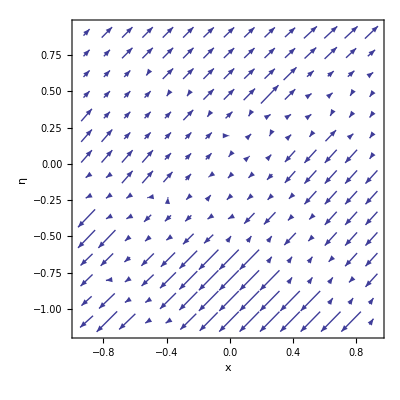

```mathematica
(* FLOW FOR BW *)
dflow=Transpose[{Transpose[{ηdata,xQdata}],Transpose[{vηdata,vxQdata}]}];
ListVectorPlot[dflow,
PlotRange->All,
FrameLabel->{Style["x",Bold,Italic,FontSize->18],Style["η",Bold,Italic,FontSize->18]},
(*FrameTicks->None,*)
(*VectorColorFunction->"Rainbow",*)
PerformanceGoal:>"Quality"]
```

```mathematica
(*FLOW FOR HO*)
dflow=Transpose[{Transpose[{xQdata,ηdata}],Transpose[{vxQdata,vηdata}]}];
ListVectorPlot[dflow,
PlotRange->All,
FrameLabel->{Style["x",Bold,Italic,FontSize->18],Style["η",Bold,Italic,FontSize->18]},
(*FrameTicks->None,*)
(*VectorColorFunction->"Rainbow",*)
PerformanceGoal:>"Quality"]
```

Transpose::nmtx: The first two levels of the one-dimensional list {xQdata, ηdata} cannot be transposed.

Transpose::nmtx: The first two levels of the one-dimensional list {vxQdata, vηdata} cannot be transposed.

Transpose::nmtx: The first two levels of the one-dimensional list {Transpose[{xQdata, ηdata}], Transpose[{vxQdata, vηdata}]} cannot be transposed.

General::stop: Further output of Transpose :: nmtx will be suppressed during this calculation.

Visualization`Core`ListVectorPlot::vfldata: Transpose[{Transpose[{xQdata, ηdata}], Transpose[{vxQdata, vηdata}]}] is not a valid vector field dataset or a valid list of datasets.

ListVectorPlot[Transpose[{Transpose[{xQdata,ηdata}],Transpose[{vxQdata,vηdata}]}],PlotRange→All,FrameLabel→{x,η},PerformanceGoal:>Quality]

```mathematica
(*ListStreamPlot[dflow,
PlotRange->All,AxesLabel->{"x","η"},
PerformanceGoal:>"Quality"]*)
```